```mathematica
(*data visualazation*)
SetDirectory[FileNameJoin[{NotebookDirectory[],"motile-QS","celldata"}]];
Dirs=FileNames[];
lenGrid=40;
plotlist={};
occupyfreq=Table[0,{i,1,lenGrid},{j,lenGrid}];
Do[data=Import[FileNameJoin[{NotebookDirectory[],"motile-QS","celldata",Dirs[[t]]}]];
celltype1=Select[data,#[[5;;6]]=={1,0}&];
celltype2=Select[data,#[[5;;6]]=={0,1}&];
t1pos=Take[celltype1,All,{2,3}];
t1matrix=Table[If[MemberQ[t1pos,{i,j}]==True,1,0],{i,1,lenGrid},{j,lenGrid}];
t2pos=Take[celltype2,All,{2,3}];
t2matrix=Table[If[MemberQ[t2pos,{i,j}]==True,2,0],{i,1,lenGrid},{j,lenGrid}];
t2matrix1=Table[If[MemberQ[t2pos,{i,j}]==True,1,0],{i,1,lenGrid},{j,lenGrid}];
tmatrix=t1matrix+t2matrix1;
occupyfreq=occupyfreq+tmatrix;
plot=Show[ArrayPlot[t1matrix+t2matrix,ColorRules->{0->Black,1->Cyan,2->Yellow}]];
Export[FileNameJoin[{NotebookDirectory[],"motile-QS","plot"<>StringTake[Dirs[[t]],{First@First@StringPosition[Dirs[[t]],"x"]+1,First@First@StringPosition[Dirs[[t]],"."]-1}]<>".tif"}],plot];
,{t,1,Length@Dirs}];
```

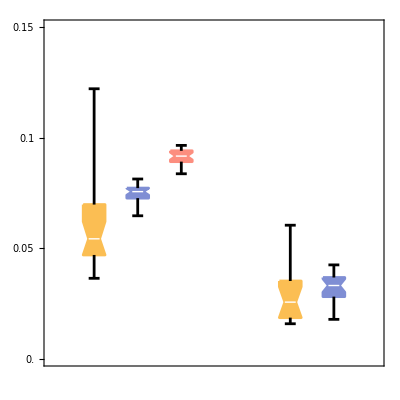

TTest::nortst: {0.267411,0.0000798748} 中至少有一个通过正态性检验得到的 p 值低于 0.025. {T} 中的检验要求数据服从正态分布.

0.189069

TTest::nortst: {0.832464,0.0000798748} 中至少有一个通过正态性检验得到的 p 值低于 0.025. {T} 中的检验要求数据服从正态分布.

0.000596665

1.57018×10^-16

0.698097

```mathematica
popgroexp=First@ToExpression@Import[FileNameJoin[{NotebookDirectory[],"popgrowthlist.xlsx"}]];
popexpQS=popgroexp[[1]];
popexpNM=popgroexp[[2,1;;14]];
popsimQS=Flatten@Import[FileNameJoin[{NotebookDirectory[],"motileQS-Popgro.csv"}]];
popsimM=Flatten@Import[FileNameJoin[{NotebookDirectory[],"motile-Popgro.csv"}]];
popsimNM=Flatten@Import[FileNameJoin[{NotebookDirectory[],"nonmotile-Popgro.csv"}]];
popplotdata={{popexpQS,popsimQS,popsimM},{popexpNM,popsimNM}};
popplot1=BoxWhiskerChart[popplotdata,{"Notched",{"Whiskers",Thickness[0.005]},{"Fences",Thickness[0.005]}},ChartBaseStyle->EdgeForm[Thickness[0.005]],BarSpacing->{1,2},PlotRange->{0,0.15},ChartStyle->{RGBColor[251/255,190/255,83/255],RGBColor[127/255,142/255,212/255],RGBColor[252/255,142/255,127/255]},FrameStyle->Directive[Thickness[0.008],30,Black],FrameTicks->{{{#,#,{0.02,0}}&/@Range[0,0.15,0.05],None},{{None,None}}},AspectRatio->1,ImageSize->400]
TTest[{popsimQS,popexpQS}]
TTest[{popsimM,popexpQS}]
TTest[{popsimM,popsimQS}]
TTest[{popsimNM,popexpNM}]
```

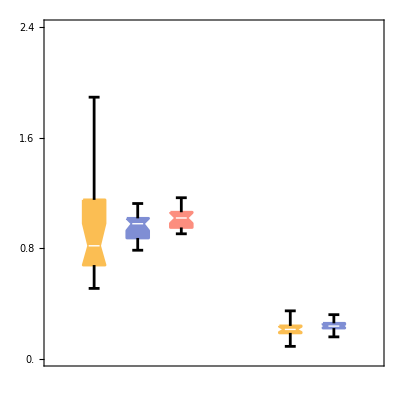

TTest::nortst: {0.348104,0.011472} 中至少有一个通过正态性检验得到的 p 值低于 0.025. {T} 中的检验要求数据服从正态分布.

0.99924

TTest::nortst: {0.920901,0.011472} 中至少有一个通过正态性检验得到的 p 值低于 0.025. {T} 中的检验要求数据服从正态分布.

0.426336

0.0267144

0.276812

```mathematica
mixexpQS=ToExpression@Import[FileNameJoin[{NotebookDirectory[],"popmixlist.xlsx"}]][[1]];
mixexpQS=Table[Last@DeleteCases[mixexpQS[[i]],Null],{i,1,Length@mixexpQS}];
mixexpNM=ToExpression@Import[FileNameJoin[{NotebookDirectory[],"popmixlist.xlsx"}]][[2]];
mixexpNM=Table[Last@DeleteCases[mixexpNM[[i]],Null],{i,1,Length@mixexpNM}];
mixsimQS=Flatten@Import[FileNameJoin[{NotebookDirectory[],"motileQS-mixing.csv"}]];
mixsimM=Flatten@Import[FileNameJoin[{NotebookDirectory[],"motile-mixing.csv"}]];
mixsimNM=Flatten@Import[FileNameJoin[{NotebookDirectory[],"nonmotile-mixing.csv"}]];
mixplotdata={{mixexpQS,mixsimQS,mixsimM},{mixexpNM,mixsimNM}};
popplot2=BoxWhiskerChart[mixplotdata,{"Notched",{"Whiskers",Thickness[0.005]},{"Fences",Thickness[0.005]}},ChartBaseStyle->EdgeForm[Thickness[0.005]],BarSpacing->{1,2},PlotRange->{0,2.4},ChartStyle->{RGBColor[251/255,190/255,83/255],RGBColor[127/255,142/255,212/255],RGBColor[252/255,142/255,127/255]},FrameStyle->Directive[Thickness[0.008],30,Black],FrameTicks->{{{#,#,{0.02,0}}&/@Range[0,2.4,0.8],None},{{None,None}}},AspectRatio->1,ImageSize->400]
TTest[{mixsimQS,mixexpQS}]
TTest[{mixsimM,mixexpQS}]
TTest[{mixsimM,mixsimQS}]
TTest[{mixsimNM,mixexpNM}]
```

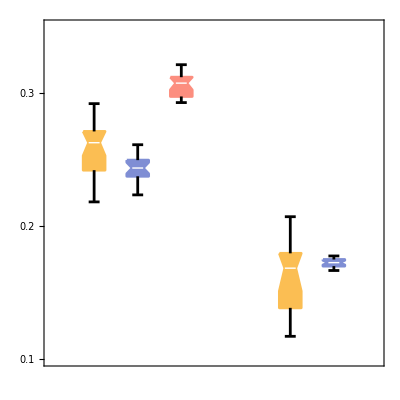

0.00532423

2.23399×10^-11

6.69884×10^-23

0.175064

```mathematica
cellgroexp=First@ToExpression@Import[FileNameJoin[{NotebookDirectory[],"singlecellgrowth.xlsx"}]];
cellexpQS=cellgroexp[[1]];
cellexpNM=cellgroexp[[2,1;;14]];
cellsimQS=Flatten@Take[Import[FileNameJoin[{NotebookDirectory[],"motileQS-Cellgro.csv"}]],All,1];
cellsimM=Flatten@Take[Import[FileNameJoin[{NotebookDirectory[],"motile-Cellgro.csv"}]],All,1];
cellsimNM=Flatten@Take[Import[FileNameJoin[{NotebookDirectory[],"nonmotile-Cellgro.csv"}]],All,1];
cellplotdata={{cellexpQS,cellsimQS,cellsimM},{cellexpNM,cellsimNM}};
popplot3=BoxWhiskerChart[cellplotdata,{"Notched",{"Whiskers",Thickness[0.005]},{"Fences",Thickness[0.005]}},ChartBaseStyle->EdgeForm[Thickness[0.005]],BarSpacing->{1,2},PlotRange->{0.1,0.35},ChartStyle->{RGBColor[251/255,190/255,83/255],RGBColor[127/255,142/255,212/255],RGBColor[252/255,142/255,127/255]},FrameStyle->Directive[Thickness[0.008],30,Black],FrameTicks->{{{#,#,{0.02,0}}&/@Range[0,0.4,0.1],None},{{None,None}}},AspectRatio->1,ImageSize->400]
TTest[{cellsimQS,cellexpQS}]
TTest[{cellsimM,cellexpQS}]
TTest[{cellsimM,cellsimQS}]
TTest[{cellsimNM,cellexpNM}]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"plot","cellgrowth.eps"}],popplot3];
Export[FileNameJoin[{NotebookDirectory[],"plot","popgrowth.eps"}],popplot1];
Export[FileNameJoin[{NotebookDirectory[],"plot","mixing.eps"}],popplot2];
```